```mathematica
+++
```

This is to compare the noise propagation from regulator to regulated gene with a unregulated gene

## Ordering data

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/2uniNoisePropReg/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
dataUnR=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlUnRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataActΔAB=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/2uniNoisePropReg/outData2/controlActGA_BsampleΔA_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataActΔBB=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/2uniNoisePropReg/outData2/controlActGA_BsampleΔB_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataInhΔBB=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/2uniNoisePropReg/outData2/controlInhGA_BsampleΔB_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataR//Dimensions
```

{500}

```mathematica
(dataAIΔA[[#]]//Dimensions)&/@Range[1,500]
```

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Table[Moment[i,j],{j,10}]→{7},Table[CentralMoment[i,j],{j,10}]→{8}|>

```mathematica
dataUnRmRNAFF=dataUnR[[All,All,1,1]];
dataUnRproteinFF=dataUnR[[All,All,2,1]];
dataUnRmRNACV2=dataUnR[[All,All,1,3]];
dataUnRproteinCV2=dataUnR[[All,All,2,3]];
dataUnRmRNAMean=dataUnR[[All,All,1,4]];
dataUnRproteinMean=dataUnR[[All,All,2,4]];
```

```mathematica
dataActΔABmRNAFF=dataActΔAB[[All,All,1,1]];
dataActΔABproteinFF=dataActΔAB[[All,All,2,1]];
dataActΔABmRNACV2=dataActΔAB[[All,All,1,3]];
dataActΔABproteinCV2=dataActΔAB[[All,All,2,3]];
dataActΔABmRNAMean=dataActΔAB[[All,All,1,4]];
dataActΔABproteinMean=dataActΔAB[[All,All,2,4]];
```

```mathematica
dataActΔBBmRNAFF=dataActΔBB[[All,All,1,1]];
dataActΔBBproteinFF=dataActΔBB[[All,All,2,1]];
dataActΔBBmRNACV2=dataActΔBB[[All,All,1,3]];
dataActΔBBproteinCV2=dataActΔBB[[All,All,2,3]];
dataActΔBBmRNAMean=dataActΔBB[[All,All,1,4]];
dataActΔBBproteinMean=dataActΔBB[[All,All,2,4]];
```

```mathematica
dataInhΔBBmRNAFF=dataInhΔBB[[All,All,1,1]];
dataInhΔBBproteinFF=dataInhΔBB[[All,All,2,1]];
dataInhΔBBmRNACV2=dataInhΔBB[[All,All,1,3]];
dataInhΔBBproteinCV2=dataInhΔBB[[All,All,2,3]];
dataInhΔBBmRNAMean=dataInhΔBB[[All,All,1,4]];
dataInhΔBBproteinMean=dataInhΔBB[[All,All,2,4]];
```

## Plots

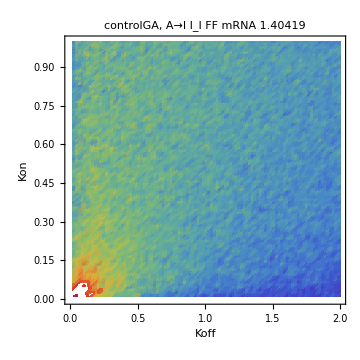
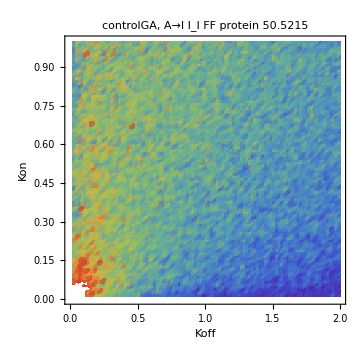
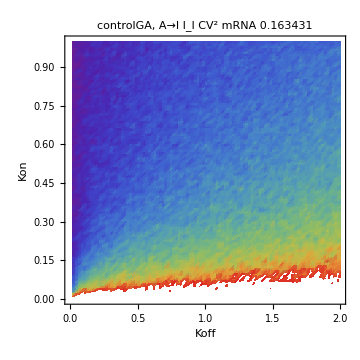
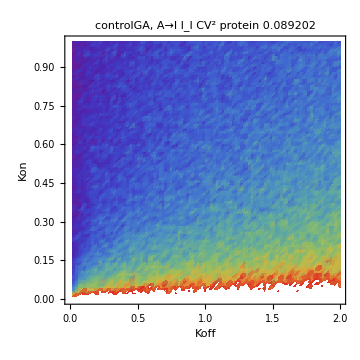
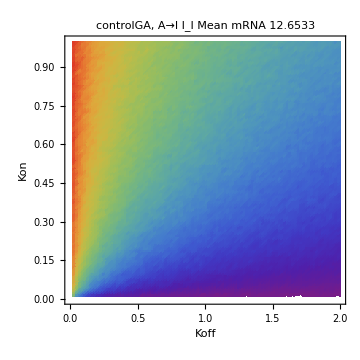
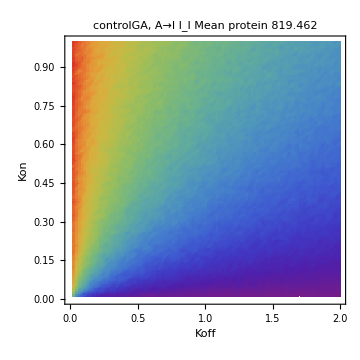
```mathematica
plotsABActΔBB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

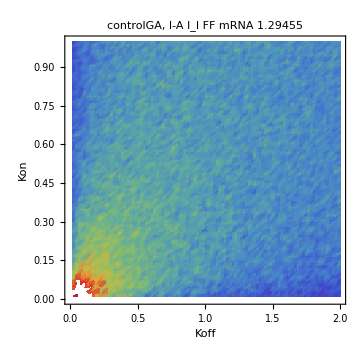
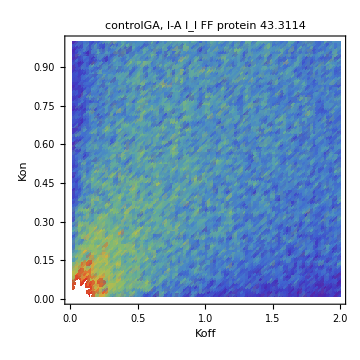
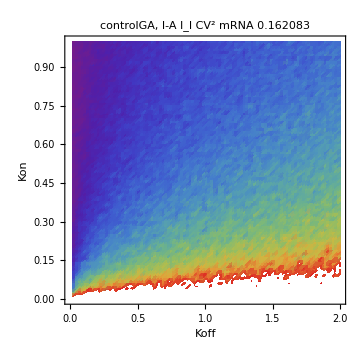
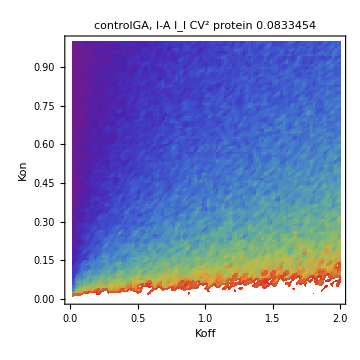
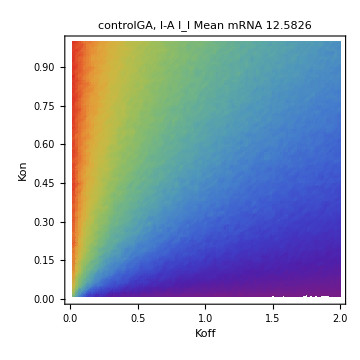
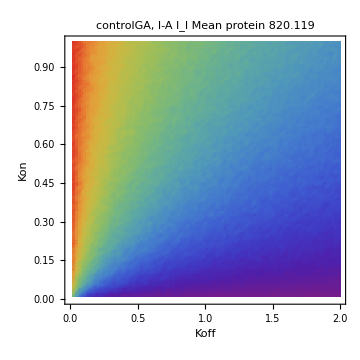
```mathematica
plotsABInhΔBB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

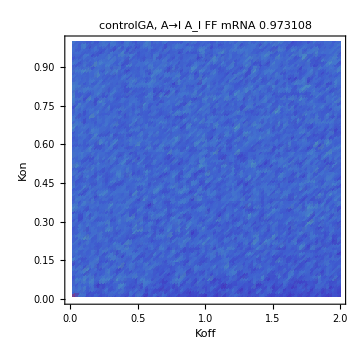
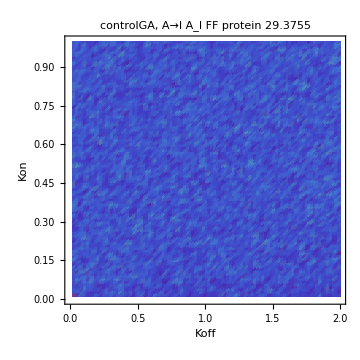
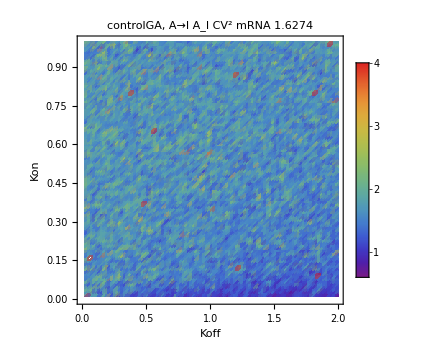
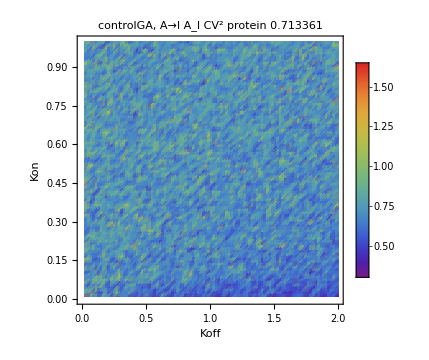
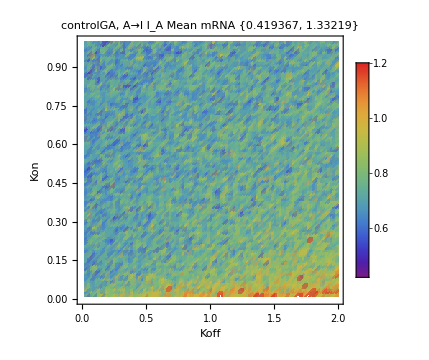
```mathematica
plotsABActΔAB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
plotsABInhΔAB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## Testing normality for dataActABΔBB

```mathematica
(***Testing if the replicates are normally distribute to apply t-test dataR*)
```

```mathematica
(*FF*************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNAFF[[RandomSample[Range[1,500],10]]]
```

<|{0.3,1.92}→-Graphics-,{0.38,1.48}→-Graphics-,{0.6,1.56}→-Graphics-,{0.41,1.34}→-Graphics-,{0.91,2.}→-Graphics-,{0.49,1.14}→-Graphics-,{0.81,0.02}→-Graphics-,{0.02,1.7}→-Graphics-,{0.45,0.26}→-Graphics-,{0.68,1.5}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinFF[[RandomSample[Range[1,500],10]]]
```

<|{0.08,0.42}→-Graphics-,{0.48,1.84}→-Graphics-,{0.41,1.34}→-Graphics-,{0.07,1.04}→-Graphics-,{0.36,0.16}→-Graphics-,{0.33,0.66}→-Graphics-,{0.01,1.54}→-Graphics-,{0.87,1.1}→-Graphics-,{0.91,1.48}→-Graphics-,{0.98,0.24}→-Graphics-|>

```mathematica
(*CV2*****************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNACV2[[RandomSample[Range[1,500],10]]]
```

<|{0.61,1.52}→-Graphics-,{0.18,1.04}→-Graphics-,{0.99,0.44}→-Graphics-,{0.78,1.34}→-Graphics-,{0.01,0.38}→-Graphics-,{0.82,0.5}→-Graphics-,{0.85,1.66}→-Graphics-,{0.21,1.72}→-Graphics-,{0.8,0.44}→-Graphics-,{0.82,1.58}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinCV2[[RandomSample[Range[1,500],10]]]
```

<|{0.61,0.2}→-Graphics-,{0.31,0.98}→-Graphics-,{0.6,0.28}→-Graphics-,{0.94,1.42}→-Graphics-,{0.18,1.48}→-Graphics-,{0.86,0.5}→-Graphics-,{0.05,0.6}→-Graphics-,{0.59,0.02}→-Graphics-,{0.98,0.24}→-Graphics-,{0.56,1.06}→-Graphics-|>

```mathematica
(*Mean*******************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNAMean[[RandomSample[Range[1,500],10]]]
```

<|{0.7,0.2}→-Graphics-,{0.01,1.8}→-Graphics-,{0.68,1.88}→-Graphics-,{0.42,1.62}→-Graphics-,{0.01,1.44}→-Graphics-,{0.62,1.84}→-Graphics-,{0.21,1.26}→-Graphics-,{0.77,2.}→-Graphics-,{0.12,1.96}→-Graphics-,{0.08,1.32}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinMean[[RandomSample[Range[1,500],10]]]
```

<|{0.41,1.2}→-Graphics-,{0.73,0.6}→-Graphics-,{0.85,1.66}→-Graphics-,{0.52,1.76}→-Graphics-,{0.59,0.84}→-Graphics-,{0.82,1.58}→-Graphics-,{0.18,0.58}→-Graphics-,{0.29,0.98}→-Graphics-,{0.78,0.96}→-Graphics-,{0.51,0.78}→-Graphics-|>

## Comparing dataUnR with regulated gene in Activation and Inactivation regulation type Δ regulated parameters

```mathematica
(************MannWhitneyTest is equal to the Wilcoxon para muestras no pareadas - pareado es que cada punto de la muestra uno se relaciona con un punto de la muestra dos. En este caso no son pareadas porque ambas muestras son las replicas aleatorias de un set de parámetros*)
```

```mathematica
GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;4]],1],MannWhitneyTest[{dataUnRproteinMean[[#]],dataActΔBBmRNAFF[[#]]}]&/@Range[1,400]}]//Association,#>0.05&]
```

<|False→<|{0.06,0.06}→2.56214×10^-34,{0.01,0.38}→2.56214×10^-34,{0.05,0.6}→2.56214×10^-34,{0.05,0.74}→2.56214×10^-34,{0.07,0.9}→2.56214×10^-34,{0.02,1.06}→2.56214×10^-34,{0.07,1.38}→2.56214×10^-34,{0.02,1.56}→2.56214×10^-34,{0.1,1.74}→2.56214×10^-34,{0.04,1.9}→2.56214×10^-34,{0.19,0.04}→2.56214×10^-34,{0.18,0.4}→2.56214×10^-34,{0.18,0.58}→2.56214×10^-34,{0.14,0.7}→2.56214×10^-34,{0.15,1.}→2.56214×10^-34,{0.2,1.14}→2.56214×10^-34,{0.18,1.32}→2.56214×10^-34,{0.16,1.44}→2.56214×10^-34,{0.2,1.74}→2.56214×10^-34,{0.18,1.9}→2.56214×10^-34,{0.24,0.18}→2.56214×10^-34,{0.29,0.3}→2.56214×10^-34,{0.21,0.5}→2.56214×10^-34,{0.23,0.7}→2.56214×10^-34,{0.28,0.84}→2.56214×10^-34,{0.25,1.12}→2.56214×10^-34,{0.22,1.38}→2.56214×10^-34,{0.29,1.44}→2.56214×10^-34,{0.24,1.78}→2.56214×10^-34,{0.22,1.96}→2.56214×10^-34,{0.38,0.12}→2.56214×10^-34,{0.4,0.22}→2.56214×10^-34,{0.33,0.58}→2.56214×10^-34,{0.38,0.64}→2.56214×10^-34,{0.35,0.86}→2.56214×10^-34,{0.31,1.04}→2.56214×10^-34,{0.39,1.3}→2.56214×10^-34,{0.39,1.52}→2.56214×10^-34,{0.39,1.64}→2.56214×10^-34,{0.34,1.88}→2.56214×10^-34,{0.5,0.12}→2.56214×10^-34,{0.44,0.32}→2.56214×10^-34,{0.48,0.54}→2.56214×10^-34,{0.47,0.72}→2.56214×10^-34,{0.48,0.94}→2.56214×10^-34,{0.41,1.2}→2.56214×10^-34,{0.47,1.38}→2.56214×10^-34,{0.42,1.58}→2.56214×10^-34,{0.48,1.76}→2.56214×10^-34,{0.47,1.88}→2.56214×10^-34,{0.58,0.2}→2.56214×10^-34,{0.58,0.26}→2.56214×10^-34,{0.59,0.52}→2.56214×10^-34,{0.55,0.74}→2.56214×10^-34,{0.6,0.86}→2.56214×10^-34,{0.54,1.04}→2.56214×10^-34,{0.58,1.38}→2.56214×10^-34,{0.52,1.56}→2.56214×10^-34,{0.57,1.8}→2.56214×10^-34,{0.56,1.94}→2.56214×10^-34,{0.7,0.2}→2.56214×10^-34,{0.66,0.38}→2.56214×10^-34,{0.65,0.56}→2.56214×10^-34,{0.68,0.64}→2.56214×10^-34,{0.66,0.82}→2.56214×10^-34,{0.66,1.18}→2.56214×10^-34,{0.7,1.32}→2.56214×10^-34,{0.61,1.52}→2.56214×10^-34,{0.7,1.8}→2.56214×10^-34,{0.65,1.86}→2.56214×10^-34,{0.73,0.08}→2.56214×10^-34,{0.79,0.32}→2.56214×10^-34,{0.8,0.44}→2.56214×10^-34,{0.73,0.78}→2.56214×10^-34,{0.75,0.82}→2.56214×10^-34,{0.76,1.02}→2.56214×10^-34,{0.78,1.34}→2.56214×10^-34,{0.71,1.6}→2.56214×10^-34,{0.78,1.66}→2.56214×10^-34,{0.78,2.}→2.56214×10^-34,{0.81,0.02}→2.56214×10^-34,{0.88,0.3}→2.56214×10^-34,{0.83,0.6}→2.56214×10^-34,{0.89,0.66}→2.56214×10^-34,{0.9,1.}→2.56214×10^-34,{0.89,1.08}→2.56214×10^-34,{0.87,1.38}→2.56214×10^-34,{0.83,1.46}→2.56214×10^-34,{0.84,1.62}→2.56214×10^-34,{0.81,1.82}→2.56214×10^-34,{1.,0.02}→2.56214×10^-34,{0.98,0.24}→2.56214×10^-34,{0.99,0.56}→2.56214×10^-34,{0.98,0.8}→2.56214×10^-34,{0.98,0.82}→2.56214×10^-34,{0.98,1.1}→2.56214×10^-34,{0.93,1.22}→2.56214×10^-34,{0.97,1.56}→2.56214×10^-34,{0.97,1.66}→2.56214×10^-34,{1.,2.}→2.56214×10^-34,{0.05,0.2}→2.56214×10^-34,{0.02,0.3}→2.56214×10^-34,{0.05,0.58}→2.56214×10^-34,{0.02,0.66}→2.56214×10^-34,{0.05,0.84}→2.56214×10^-34,{0.05,1.08}→2.56214×10^-34,{0.09,1.36}→2.56214×10^-34,{0.01,1.44}→2.56214×10^-34,{0.09,1.66}→2.56214×10^-34,{0.07,1.96}→2.56214×10^-34,{0.2,0.14}→2.56214×10^-34,{0.17,0.24}→2.56214×10^-34,{0.13,0.5}→2.56214×10^-34,{0.17,0.66}→2.56214×10^-34,{0.16,0.94}→2.56214×10^-34,{0.18,1.16}→2.56214×10^-34,{0.19,1.38}→2.56214×10^-34,{0.18,1.52}→2.56214×10^-34,{0.13,1.7}→2.56214×10^-34,{0.18,1.94}→2.56214×10^-34,{0.27,0.18}→2.56214×10^-34,{0.25,0.26}→2.56214×10^-34,{0.3,0.6}→2.56214×10^-34,{0.22,0.76}→2.56214×10^-34,{0.29,0.9}→2.56214×10^-34,{0.24,1.18}→2.56214×10^-34,{0.21,1.26}→2.56214×10^-34,{0.23,1.58}→2.56214×10^-34,{0.26,1.74}→2.56214×10^-34,{0.26,1.84}→2.56214×10^-34,{0.39,0.18}→2.56214×10^-34,{0.34,0.32}→2.56214×10^-34,{0.31,0.54}→2.56214×10^-34,{0.34,0.68}→2.56214×10^-34,{0.31,0.98}→2.56214×10^-34,{0.34,1.1}→2.56214×10^-34,{0.36,1.22}→2.56214×10^-34,{0.35,1.48}→2.56214×10^-34,{0.31,1.62}→2.56214×10^-34,{0.39,1.94}→2.56214×10^-34,{0.47,0.06}→2.56214×10^-34,{0.43,0.36}→2.56214×10^-34,{0.41,0.52}→2.56214×10^-34,{0.49,0.8}→2.56214×10^-34,{0.45,0.96}→2.56214×10^-34,{0.44,1.16}→2.56214×10^-34,{0.48,1.32}→2.56214×10^-34,{0.48,1.52}→2.56214×10^-34,{0.49,1.62}→2.56214×10^-34,{0.42,1.86}→2.56214×10^-34,{0.55,0.02}→2.56214×10^-34,{0.6,0.28}→2.56214×10^-34,{0.54,0.6}→2.56214×10^-34,{0.51,0.78}→2.56214×10^-34,{0.6,0.98}→2.56214×10^-34,{0.51,1.2}→2.56214×10^-34,{0.56,1.24}→2.56214×10^-34,{0.56,1.6}→2.56214×10^-34,{0.55,1.72}→2.56214×10^-34,{0.51,1.88}→2.56214×10^-34,{0.61,0.16}→2.56214×10^-34,{0.67,0.22}→2.56214×10^-34,{0.65,0.58}→2.56214×10^-34,{0.67,0.62}→2.56214×10^-34,{0.65,0.94}→2.56214×10^-34,{0.63,1.18}→2.56214×10^-34,{0.65,1.32}→2.56214×10^-34,{0.68,1.5}→2.56214×10^-34,{0.7,1.68}→2.56214×10^-34,{0.67,1.94}→2.56214×10^-34,{0.77,0.06}→2.56214×10^-34,{0.77,0.32}→2.56214×10^-34,{0.76,0.44}→2.56214×10^-34,{0.76,0.8}→2.56214×10^-34,{0.78,0.96}→2.56214×10^-34,{0.73,1.08}→2.56214×10^-34,{0.74,1.32}→2.56214×10^-34,{0.77,1.44}→2.56214×10^-34,{0.75,1.68}→2.56214×10^-34,{0.8,1.9}→2.56214×10^-34,{0.89,0.12}→2.56214×10^-34,{0.85,0.28}→2.56214×10^-34,{0.89,0.5}→2.56214×10^-34,{0.86,0.68}→2.56214×10^-34,{0.9,0.98}→2.56214×10^-34,{0.87,1.1}→2.56214×10^-34,{0.88,1.4}→2.56214×10^-34,{0.84,1.52}→2.56214×10^-34,{0.9,1.66}→2.56214×10^-34,{0.86,1.92}→2.56214×10^-34,{0.93,0.1}→2.56214×10^-34,{0.94,0.38}→2.56214×10^-34,{0.91,0.56}→2.56214×10^-34,{0.95,0.66}→2.56214×10^-34,{0.98,0.98}→2.56214×10^-34,{0.98,1.14}→2.56214×10^-34,{0.99,1.34}→2.56214×10^-34,{0.94,1.42}→2.56214×10^-34,{0.92,1.74}→2.56214×10^-34,{0.96,1.98}→2.56214×10^-34,{0.09,0.1}→2.56214×10^-34,{0.08,0.24}→2.56214×10^-34,{0.09,0.5}→2.56214×10^-34,{0.09,0.68}→2.56214×10^-34,{0.08,0.9}→2.56214×10^-34,{0.04,1.04}→2.56214×10^-34,{0.08,1.36}→2.56214×10^-34,{0.06,1.52}→2.56214×10^-34,{0.09,1.64}→2.56214×10^-34,{0.04,1.92}→2.56214×10^-34,{0.11,0.04}→2.56214×10^-34,{0.16,0.36}→2.56214×10^-34,{0.19,0.48}→2.56214×10^-34,{0.16,0.78}→2.56214×10^-34,{0.12,1.}→2.56214×10^-34,{0.18,1.12}→2.56214×10^-34,{0.19,1.28}→2.56214×10^-34,{0.19,1.52}→2.56214×10^-34,{0.13,1.72}→2.56214×10^-34,{0.19,1.94}→2.56214×10^-34,{0.22,0.18}→2.56214×10^-34,{0.26,0.3}→2.56214×10^-34,{0.25,0.58}→2.56214×10^-34,{0.29,0.7}→2.56214×10^-34,{0.23,0.86}→2.56214×10^-34,{0.24,1.14}→2.56214×10^-34,{0.26,1.26}→2.56214×10^-34,{0.23,1.56}→2.56214×10^-34,{0.29,1.72}→2.56214×10^-34,{0.3,1.92}→2.56214×10^-34,{0.36,0.16}→2.56214×10^-34,{0.32,0.3}→2.56214×10^-34,{0.38,0.52}→2.56214×10^-34,{0.37,0.76}→2.56214×10^-34,{0.39,0.9}→2.56214×10^-34,{0.36,1.06}→2.56214×10^-34,{0.36,1.4}→2.56214×10^-34,{0.39,1.5}→2.56214×10^-34,{0.31,1.7}→2.56214×10^-34,{0.36,1.88}→2.56214×10^-34,{0.41,0.2}→2.56214×10^-34,{0.47,0.34}→2.56214×10^-34,{0.41,0.58}→2.56214×10^-34,{0.43,0.8}→2.56214×10^-34,{0.48,1.}→2.56214×10^-34,{0.44,1.18}→2.56214×10^-34,{0.42,1.28}→2.56214×10^-34,{0.45,1.44}→2.56214×10^-34,{0.47,1.74}→2.56214×10^-34,{0.48,1.84}→2.56214×10^-34,{0.56,0.18}→2.56214×10^-34,{0.52,0.32}→2.56214×10^-34,{0.56,0.42}→2.56214×10^-34,{0.54,0.7}→2.56214×10^-34,{0.59,0.82}→2.56214×10^-34,{0.54,1.12}→2.56214×10^-34,{0.57,1.26}→2.56214×10^-34,{0.57,1.42}→2.56214×10^-34,{0.52,1.76}→2.56214×10^-34,{0.53,1.98}→2.56214×10^-34,{0.66,0.02}→2.56214×10^-34,{0.65,0.28}→2.56214×10^-34,{0.63,0.48}→2.56214×10^-34,{0.61,0.7}→2.56214×10^-34,{0.7,0.98}→2.56214×10^-34,{0.65,1.04}→2.56214×10^-34,{0.65,1.22}→2.56214×10^-34,{0.65,1.44}→2.56214×10^-34,{0.61,1.64}→2.56214×10^-34,{0.69,1.9}→2.56214×10^-34,{0.78,0.06}→2.56214×10^-34,{0.74,0.32}→2.56214×10^-34,{0.73,0.6}→2.56214×10^-34,{0.77,0.68}→2.56214×10^-34,{0.79,0.88}→2.56214×10^-34,{0.78,1.1}→2.56214×10^-34,{0.74,1.4}→2.56214×10^-34,{0.8,1.46}→2.56214×10^-34,{0.71,1.74}→2.56214×10^-34,{0.79,1.96}→2.56214×10^-34,{0.9,0.12}→2.56214×10^-34,{0.87,0.24}→2.56214×10^-34,{0.84,0.58}→2.56214×10^-34,{0.84,0.62}→2.56214×10^-34,{0.83,0.98}→2.56214×10^-34,{0.9,1.06}→2.56214×10^-34,{0.82,1.3}→2.56214×10^-34,{0.87,1.5}→2.56214×10^-34,{0.85,1.66}→2.56214×10^-34,{0.81,1.84}→2.56214×10^-34,{0.93,0.16}→2.56214×10^-34,{0.94,0.24}→2.56214×10^-34,{0.99,0.44}→2.56214×10^-34,{0.97,0.66}→2.56214×10^-34,{0.95,0.96}→2.56214×10^-34,{0.94,1.1}→2.56214×10^-34,{0.91,1.22}→2.56214×10^-34,{0.92,1.48}→2.56214×10^-34,{0.96,1.68}→2.56214×10^-34,{0.91,2.}→2.56214×10^-34,{0.07,0.02}→2.56214×10^-34,{0.08,0.28}→2.56214×10^-34,{0.08,0.42}→2.56214×10^-34,{0.1,0.64}→2.56214×10^-34,{0.09,1.}→2.56214×10^-34,{0.04,1.12}→2.56214×10^-34,{0.06,1.3}→2.56214×10^-34,{0.08,1.54}→2.56214×10^-34,{0.02,1.7}→2.56214×10^-34,{0.06,1.9}→2.56214×10^-34,{0.13,0.16}→2.56214×10^-34,{0.16,0.26}→2.56214×10^-34,{0.11,0.48}→2.56214×10^-34,{0.12,0.72}→2.56214×10^-34,{0.15,0.98}→2.56214×10^-34,{0.18,1.04}→2.56214×10^-34,{0.12,1.28}→2.56214×10^-34,{0.14,1.46}→2.56214×10^-34,{0.12,1.62}→2.56214×10^-34,{0.12,2.}→2.56214×10^-34,{0.25,0.02}→2.56214×10^-34,{0.28,0.34}→2.56214×10^-34,{0.23,0.5}→2.56214×10^-34,{0.26,0.78}→2.56214×10^-34,{0.26,1.}→2.56214×10^-34,{0.26,1.06}→2.56214×10^-34,{0.3,1.22}→2.56214×10^-34,{0.27,1.6}→2.56214×10^-34,{0.21,1.72}→2.56214×10^-34,{0.27,1.88}→2.56214×10^-34,{0.38,0.08}→2.56214×10^-34,{0.35,0.22}→2.56214×10^-34,{0.36,0.48}→2.56214×10^-34,{0.39,0.78}→2.56214×10^-34,{0.31,0.86}→2.56214×10^-34,{0.31,1.18}→2.56214×10^-34,{0.35,1.3}→2.56214×10^-34,{0.38,1.48}→2.56214×10^-34,{0.33,1.8}→2.56214×10^-34,{0.34,1.86}→2.56214×10^-34,{0.42,0.2}→2.56214×10^-34,{0.41,0.4}→2.56214×10^-34,{0.42,0.46}→2.56214×10^-34,{0.47,0.68}→2.56214×10^-34,{0.43,0.96}→2.56214×10^-34,{0.49,1.14}→2.56214×10^-34,{0.41,1.34}→2.56214×10^-34,{0.45,1.52}→2.56214×10^-34,{0.44,1.64}→2.56214×10^-34,{0.41,1.9}→2.56214×10^-34,{0.54,0.2}→2.56214×10^-34,{0.58,0.4}→2.56214×10^-34,{0.57,0.58}→2.56214×10^-34,{0.52,0.8}→2.56214×10^-34,{0.55,0.98}→2.56214×10^-34,{0.53,1.08}→2.56214×10^-34,{0.52,1.28}→2.56214×10^-34,{0.6,1.56}→2.56214×10^-34,{0.54,1.8}→2.56214×10^-34,{0.57,1.88}→2.56214×10^-34,{0.61,0.2}→2.56214×10^-34,{0.62,0.28}→2.56214×10^-34,{0.67,0.46}→2.56214×10^-34,{0.69,0.74}→2.56214×10^-34,{0.7,0.94}→2.56214×10^-34,{0.64,1.2}→2.56214×10^-34,{0.63,1.26}→2.56214×10^-34,{0.7,1.46}→2.56214×10^-34,{0.61,1.72}→2.56214×10^-34,{0.62,1.84}→2.56214×10^-34,{0.77,0.18}→2.56214×10^-34,{0.8,0.28}→2.56214×10^-34,{0.75,0.52}→2.56214×10^-34,{0.73,0.74}→2.56214×10^-34,{0.8,0.84}→2.56214×10^-34,{0.77,1.02}→2.56214×10^-34,{0.79,1.26}→2.56214×10^-34,{0.74,1.52}→2.56214×10^-34,{0.72,1.68}→2.56214×10^-34,{0.8,1.94}→2.56214×10^-34,{0.86,0.02}→2.56214×10^-34,{0.83,0.3}→2.56214×10^-34,{0.82,0.5}→2.56214×10^-34,{0.87,0.76}→2.56214×10^-34,{0.85,0.98}→2.56214×10^-34,{0.86,1.14}→2.56214×10^-34,{0.83,1.38}→2.56214×10^-34,{0.82,1.58}→2.56214×10^-34,{0.83,1.68}→2.56214×10^-34,{0.85,1.94}→2.56214×10^-34,{0.99,0.06}→2.56214×10^-34,{0.93,0.24}→2.56214×10^-34,{0.95,0.46}→2.56214×10^-34,{0.99,0.76}→2.56214×10^-34,{1.,0.82}→2.56214×10^-34,{0.93,1.04}→2.56214×10^-34,{0.97,1.32}→2.56214×10^-34,{0.92,1.46}→2.56214×10^-34,{0.97,1.78}→2.56214×10^-34,{0.92,1.82}→2.56214×10^-34|>|>

```mathematica
GroupBy[MapThread[#1->#2&,{sample[[1]],MannWhitneyTest[{dataUnRproteinMean[[#]],dataActΔBBmRNAFF[[#]]}]&/@Range[1,400]}]//Association,#>0.05&]
```

<|False→<|{0.06,0.06}→2.56214×10^-34,{0.01,0.38}→2.56214×10^-34,{0.05,0.6}→2.56214×10^-34,{0.05,0.74}→2.56214×10^-34,{0.07,0.9}→2.56214×10^-34,{0.02,1.06}→2.56214×10^-34,{0.07,1.38}→2.56214×10^-34,{0.02,1.56}→2.56214×10^-34,{0.1,1.74}→2.56214×10^-34,{0.04,1.9}→2.56214×10^-34,{0.19,0.04}→2.56214×10^-34,{0.18,0.4}→2.56214×10^-34,{0.18,0.58}→2.56214×10^-34,{0.14,0.7}→2.56214×10^-34,{0.15,1.}→2.56214×10^-34,{0.2,1.14}→2.56214×10^-34,{0.18,1.32}→2.56214×10^-34,{0.16,1.44}→2.56214×10^-34,{0.2,1.74}→2.56214×10^-34,{0.18,1.9}→2.56214×10^-34,{0.24,0.18}→2.56214×10^-34,{0.29,0.3}→2.56214×10^-34,{0.21,0.5}→2.56214×10^-34,{0.23,0.7}→2.56214×10^-34,{0.28,0.84}→2.56214×10^-34,{0.25,1.12}→2.56214×10^-34,{0.22,1.38}→2.56214×10^-34,{0.29,1.44}→2.56214×10^-34,{0.24,1.78}→2.56214×10^-34,{0.22,1.96}→2.56214×10^-34,{0.38,0.12}→2.56214×10^-34,{0.4,0.22}→2.56214×10^-34,{0.33,0.58}→2.56214×10^-34,{0.38,0.64}→2.56214×10^-34,{0.35,0.86}→2.56214×10^-34,{0.31,1.04}→2.56214×10^-34,{0.39,1.3}→2.56214×10^-34,{0.39,1.52}→2.56214×10^-34,{0.39,1.64}→2.56214×10^-34,{0.34,1.88}→2.56214×10^-34,{0.5,0.12}→2.56214×10^-34,{0.44,0.32}→2.56214×10^-34,{0.48,0.54}→2.56214×10^-34,{0.47,0.72}→2.56214×10^-34,{0.48,0.94}→2.56214×10^-34,{0.41,1.2}→2.56214×10^-34,{0.47,1.38}→2.56214×10^-34,{0.42,1.58}→2.56214×10^-34,{0.48,1.76}→2.56214×10^-34,{0.47,1.88}→2.56214×10^-34,{0.58,0.2}→2.56214×10^-34,{0.58,0.26}→2.56214×10^-34,{0.59,0.52}→2.56214×10^-34,{0.55,0.74}→2.56214×10^-34,{0.6,0.86}→2.56214×10^-34,{0.54,1.04}→2.56214×10^-34,{0.58,1.38}→2.56214×10^-34,{0.52,1.56}→2.56214×10^-34,{0.57,1.8}→2.56214×10^-34,{0.56,1.94}→2.56214×10^-34,{0.7,0.2}→2.56214×10^-34,{0.66,0.38}→2.56214×10^-34,{0.65,0.56}→2.56214×10^-34,{0.68,0.64}→2.56214×10^-34,{0.66,0.82}→2.56214×10^-34,{0.66,1.18}→2.56214×10^-34,{0.7,1.32}→2.56214×10^-34,{0.61,1.52}→2.56214×10^-34,{0.7,1.8}→2.56214×10^-34,{0.65,1.86}→2.56214×10^-34,{0.73,0.08}→2.56214×10^-34,{0.79,0.32}→2.56214×10^-34,{0.8,0.44}→2.56214×10^-34,{0.73,0.78}→2.56214×10^-34,{0.75,0.82}→2.56214×10^-34,{0.76,1.02}→2.56214×10^-34,{0.78,1.34}→2.56214×10^-34,{0.71,1.6}→2.56214×10^-34,{0.78,1.66}→2.56214×10^-34,{0.78,2.}→2.56214×10^-34,{0.81,0.02}→2.56214×10^-34,{0.88,0.3}→2.56214×10^-34,{0.83,0.6}→2.56214×10^-34,{0.89,0.66}→2.56214×10^-34,{0.9,1.}→2.56214×10^-34,{0.89,1.08}→2.56214×10^-34,{0.87,1.38}→2.56214×10^-34,{0.83,1.46}→2.56214×10^-34,{0.84,1.62}→2.56214×10^-34,{0.81,1.82}→2.56214×10^-34,{1.,0.02}→2.56214×10^-34,{0.98,0.24}→2.56214×10^-34,{0.99,0.56}→2.56214×10^-34,{0.98,0.8}→2.56214×10^-34,{0.98,0.82}→2.56214×10^-34,{0.98,1.1}→2.56214×10^-34,{0.93,1.22}→2.56214×10^-34,{0.97,1.56}→2.56214×10^-34,{0.97,1.66}→2.56214×10^-34,{1.,2.}→2.56214×10^-34|>|>

```mathematica
MapAt[Reverse,%//Values//Keys,{All,All}]
```

{{{0.06,0.06},{0.38,0.01},{0.6,0.05},{0.74,0.05},{0.9,0.07},{1.06,0.02},{1.38,0.07},{1.56,0.02},{1.74,0.1},{1.9,0.04},{0.04,0.19},{0.4,0.18},{0.58,0.18},{0.7,0.14},{1.,0.15},{1.14,0.2},{1.32,0.18},{1.44,0.16},{1.74,0.2},{1.9,0.18},{0.18,0.24},{0.3,0.29},{0.5,0.21},{0.7,0.23},{0.84,0.28},{1.12,0.25},{1.38,0.22},{1.44,0.29},{1.78,0.24},{1.96,0.22},{0.12,0.38},{0.22,0.4},{0.58,0.33},{0.64,0.38},{0.86,0.35},{1.04,0.31},{1.3,0.39},{1.52,0.39},{1.64,0.39},{1.88,0.34},{0.12,0.5},{0.32,0.44},{0.54,0.48},{0.72,0.47},{0.94,0.48},{1.2,0.41},{1.38,0.47},{1.58,0.42},{1.76,0.48},{1.88,0.47},{0.2,0.58},{0.26,0.58},{0.52,0.59},{0.74,0.55},{0.86,0.6},{1.04,0.54},{1.38,0.58},{1.56,0.52},{1.8,0.57},{1.94,0.56},{0.2,0.7},{0.38,0.66},{0.56,0.65},{0.64,0.68},{0.82,0.66},{1.18,0.66},{1.32,0.7},{1.52,0.61},{1.8,0.7},{1.86,0.65},{0.08,0.73},{0.32,0.79},{0.44,0.8},{0.78,0.73},{0.82,0.75},{1.02,0.76},{1.34,0.78},{1.6,0.71},{1.66,0.78},{2.,0.78},{0.02,0.81},{0.3,0.88},{0.6,0.83},{0.66,0.89},{1.,0.9},{1.08,0.89},{1.38,0.87},{1.46,0.83},{1.62,0.84},{1.82,0.81},{0.02,1.},{0.24,0.98},{0.56,0.99},{0.8,0.98},{0.82,0.98},{1.1,0.98},{1.22,0.93},{1.56,0.97},{1.66,0.97},{2.,1.},{0.2,0.05},{0.3,0.02},{0.58,0.05},{0.66,0.02},{0.84,0.05},{1.08,0.05},{1.36,0.09},{1.44,0.01},{1.66,0.09},{1.96,0.07},{0.14,0.2},{0.24,0.17},{0.5,0.13},{0.66,0.17},{0.94,0.16},{1.16,0.18},{1.38,0.19},{1.52,0.18},{1.7,0.13},{1.94,0.18},{0.18,0.27},{0.26,0.25},{0.6,0.3},{0.76,0.22},{0.9,0.29},{1.18,0.24},{1.26,0.21},{1.58,0.23},{1.74,0.26},{1.84,0.26},{0.18,0.39},{0.32,0.34},{0.54,0.31},{0.68,0.34},{0.98,0.31},{1.1,0.34},{1.22,0.36},{1.48,0.35},{1.62,0.31},{1.94,0.39},{0.06,0.47},{0.36,0.43},{0.52,0.41},{0.8,0.49},{0.96,0.45},{1.16,0.44},{1.32,0.48},{1.52,0.48},{1.62,0.49},{1.86,0.42},{0.02,0.55},{0.28,0.6},{0.6,0.54},{0.78,0.51},{0.98,0.6},{1.2,0.51},{1.24,0.56},{1.6,0.56},{1.72,0.55},{1.88,0.51},{0.16,0.61},{0.22,0.67},{0.58,0.65},{0.62,0.67},{0.94,0.65},{1.18,0.63},{1.32,0.65},{1.5,0.68},{1.68,0.7},{1.94,0.67},{0.06,0.77},{0.32,0.77},{0.44,0.76},{0.8,0.76},{0.96,0.78},{1.08,0.73},{1.32,0.74},{1.44,0.77},{1.68,0.75},{1.9,0.8},{0.12,0.89},{0.28,0.85},{0.5,0.89},{0.68,0.86},{0.98,0.9},{1.1,0.87},{1.4,0.88},{1.52,0.84},{1.66,0.9},{1.92,0.86},{0.1,0.93},{0.38,0.94},{0.56,0.91},{0.66,0.95},{0.98,0.98},{1.14,0.98},{1.34,0.99},{1.42,0.94},{1.74,0.92},{1.98,0.96},{0.1,0.09},{0.24,0.08},{0.5,0.09},{0.68,0.09},{0.9,0.08},{1.04,0.04},{1.36,0.08},{1.52,0.06},{1.64,0.09},{1.92,0.04},{0.04,0.11},{0.36,0.16},{0.48,0.19},{0.78,0.16},{1.,0.12},{1.12,0.18},{1.28,0.19},{1.52,0.19},{1.72,0.13},{1.94,0.19},{0.18,0.22},{0.3,0.26},{0.58,0.25},{0.7,0.29},{0.86,0.23},{1.14,0.24},{1.26,0.26},{1.56,0.23},{1.72,0.29},{1.92,0.3},{0.16,0.36},{0.3,0.32},{0.52,0.38},{0.76,0.37},{0.9,0.39},{1.06,0.36},{1.4,0.36},{1.5,0.39},{1.7,0.31},{1.88,0.36},{0.2,0.41},{0.34,0.47},{0.58,0.41},{0.8,0.43},{1.,0.48},{1.18,0.44},{1.28,0.42},{1.44,0.45},{1.74,0.47},{1.84,0.48},{0.18,0.56},{0.32,0.52},{0.42,0.56},{0.7,0.54},{0.82,0.59},{1.12,0.54},{1.26,0.57},{1.42,0.57},{1.76,0.52},{1.98,0.53},{0.02,0.66},{0.28,0.65},{0.48,0.63},{0.7,0.61},{0.98,0.7},{1.04,0.65},{1.22,0.65},{1.44,0.65},{1.64,0.61},{1.9,0.69},{0.06,0.78},{0.32,0.74},{0.6,0.73},{0.68,0.77},{0.88,0.79},{1.1,0.78},{1.4,0.74},{1.46,0.8},{1.74,0.71},{1.96,0.79},{0.12,0.9},{0.24,0.87},{0.58,0.84},{0.62,0.84},{0.98,0.83},{1.06,0.9},{1.3,0.82},{1.5,0.87},{1.66,0.85},{1.84,0.81},{0.16,0.93},{0.24,0.94},{0.44,0.99},{0.66,0.97},{0.96,0.95},{1.1,0.94},{1.22,0.91},{1.48,0.92},{1.68,0.96},{2.,0.91},{0.02,0.07},{0.28,0.08},{0.42,0.08},{0.64,0.1},{1.,0.09},{1.12,0.04},{1.3,0.06},{1.54,0.08},{1.7,0.02},{1.9,0.06},{0.16,0.13},{0.26,0.16},{0.48,0.11},{0.72,0.12},{0.98,0.15},{1.04,0.18},{1.28,0.12},{1.46,0.14},{1.62,0.12},{2.,0.12},{0.02,0.25},{0.34,0.28},{0.5,0.23},{0.78,0.26},{1.,0.26},{1.06,0.26},{1.22,0.3},{1.6,0.27},{1.72,0.21},{1.88,0.27},{0.08,0.38},{0.22,0.35},{0.48,0.36},{0.78,0.39},{0.86,0.31},{1.18,0.31},{1.3,0.35},{1.48,0.38},{1.8,0.33},{1.86,0.34},{0.2,0.42},{0.4,0.41},{0.46,0.42},{0.68,0.47},{0.96,0.43},{1.14,0.49},{1.34,0.41},{1.52,0.45},{1.64,0.44},{1.9,0.41},{0.2,0.54},{0.4,0.58},{0.58,0.57},{0.8,0.52},{0.98,0.55},{1.08,0.53},{1.28,0.52},{1.56,0.6},{1.8,0.54},{1.88,0.57},{0.2,0.61},{0.28,0.62},{0.46,0.67},{0.74,0.69},{0.94,0.7},{1.2,0.64},{1.26,0.63},{1.46,0.7},{1.72,0.61},{1.84,0.62},{0.18,0.77},{0.28,0.8},{0.52,0.75},{0.74,0.73},{0.84,0.8},{1.02,0.77},{1.26,0.79},{1.52,0.74},{1.68,0.72},{1.94,0.8},{0.02,0.86},{0.3,0.83},{0.5,0.82},{0.76,0.87},{0.98,0.85},{1.14,0.86},{1.38,0.83},{1.58,0.82},{1.68,0.83},{1.94,0.85},{0.06,0.99},{0.24,0.93},{0.46,0.95},{0.76,0.99},{0.82,1.},{1.04,0.93},{1.32,0.97},{1.46,0.92},{1.78,0.97},{1.82,0.92}}}

```mathematica
SetOptions[ListPlot,ImageSize->Medium,Frame->True,FrameLabel->{"koff", "kon"}];
```

```mathematica
ListPlot[%,PlotStyle->{Black(*iguales*),Cyan(*diferentes*)}]
```

-Graphics-

```mathematica
(*********************function to get the significance plots: It is plotted the p-values in black (p-value>0.05 -> the samples have equal median) and cyan (p-value<0.05 -> the samples do not have equal median)*)
```

```mathematica
plotSignificance[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys,groups[True]//Keys},{All,All}],FrameTicksStyle->Directive[Black,15],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
plotSignificance2[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys},{All,All}],FrameTicksStyle->Directive[Black,15],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
(**********************************************************************Inh*)
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataInhΔBBmRNAFF,"UnR&R mRNA FF"},{dataUnRproteinFF,dataInhΔBBproteinFF,"UnR&R protein FF"},{dataUnRmRNACV2,dataInhΔBBmRNACV2,"UnR&R mRNA CV2"},{dataUnRproteinCV2,dataInhΔBBproteinCV2,"UnR&R protein CV2"},{dataUnRmRNAMean,dataInhΔBBmRNAMean,"UnR&R mRNA Mean"},{dataUnRproteinMean,dataInhΔBBproteinMean,"UnR&R protein Mean"}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(**********************************************************************Atc*)
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataActΔBBmRNAFF,"UnR&R mRNA FF"},{dataUnRproteinFF,dataActΔBBproteinFF,"UnR&R protein FF"},{dataUnRproteinCV2,dataActΔBBproteinCV2,"UnR&R protein CV2"},{dataUnRmRNAMean,dataActΔBBmRNAMean,"UnR&R mRNA Mean"},{dataUnRproteinMean,dataActΔBBproteinMean,"UnR&R protein Mean"}}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
Apply[plotSignificance2[#1,#2,#3]&]/@{{dataUnRmRNACV2,dataActΔBBmRNACV2,"UnR&R mRNA CV2"}}
```

{-Graphics-}

These results were not completely published in the paper. I only  share the results about FF but not about CV2 and mean of molecules. It shows the noise (CV2) in regulated gene increases as well as the mean decreases, but the noise strength is no always different (FF)

```mathematica
Show[#]&/@Transpose[{plotsABActΔBB,%510}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Comparing dataUnR with regulated gene in Activation and Inactivation regulation type Δ regulator parameters

Regulated gene express as in region 1

```mathematica
(************MannWhitneyTest is equal to the Wilcoxon para muestras no pareadas - pareado es que cada punto de la muestra uno se relaciona con un punto de la muestra dos. En este caso no son pareadas porque ambas muestras son las replicas aleatorias de un set de parámetros*)
```

```mathematica
GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;4]],1],MannWhitneyTest[{dataUnRproteinMean[[#]],dataActΔBBmRNAFF[[#]]}]&/@Range[1,400]}]//Association,#>0.05&]
```

<|False→<|{0.06,0.06}→2.56214×10^-34,{0.01,0.38}→2.56214×10^-34,{0.05,0.6}→2.56214×10^-34,{0.05,0.74}→2.56214×10^-34,{0.07,0.9}→2.56214×10^-34,{0.02,1.06}→2.56214×10^-34,{0.07,1.38}→2.56214×10^-34,{0.02,1.56}→2.56214×10^-34,{0.1,1.74}→2.56214×10^-34,{0.04,1.9}→2.56214×10^-34,{0.19,0.04}→2.56214×10^-34,{0.18,0.4}→2.56214×10^-34,{0.18,0.58}→2.56214×10^-34,{0.14,0.7}→2.56214×10^-34,{0.15,1.}→2.56214×10^-34,{0.2,1.14}→2.56214×10^-34,{0.18,1.32}→2.56214×10^-34,{0.16,1.44}→2.56214×10^-34,{0.2,1.74}→2.56214×10^-34,{0.18,1.9}→2.56214×10^-34,{0.24,0.18}→2.56214×10^-34,{0.29,0.3}→2.56214×10^-34,{0.21,0.5}→2.56214×10^-34,{0.23,0.7}→2.56214×10^-34,{0.28,0.84}→2.56214×10^-34,{0.25,1.12}→2.56214×10^-34,{0.22,1.38}→2.56214×10^-34,{0.29,1.44}→2.56214×10^-34,{0.24,1.78}→2.56214×10^-34,{0.22,1.96}→2.56214×10^-34,{0.38,0.12}→2.56214×10^-34,{0.4,0.22}→2.56214×10^-34,{0.33,0.58}→2.56214×10^-34,{0.38,0.64}→2.56214×10^-34,{0.35,0.86}→2.56214×10^-34,{0.31,1.04}→2.56214×10^-34,{0.39,1.3}→2.56214×10^-34,{0.39,1.52}→2.56214×10^-34,{0.39,1.64}→2.56214×10^-34,{0.34,1.88}→2.56214×10^-34,{0.5,0.12}→2.56214×10^-34,{0.44,0.32}→2.56214×10^-34,{0.48,0.54}→2.56214×10^-34,{0.47,0.72}→2.56214×10^-34,{0.48,0.94}→2.56214×10^-34,{0.41,1.2}→2.56214×10^-34,{0.47,1.38}→2.56214×10^-34,{0.42,1.58}→2.56214×10^-34,{0.48,1.76}→2.56214×10^-34,{0.47,1.88}→2.56214×10^-34,{0.58,0.2}→2.56214×10^-34,{0.58,0.26}→2.56214×10^-34,{0.59,0.52}→2.56214×10^-34,{0.55,0.74}→2.56214×10^-34,{0.6,0.86}→2.56214×10^-34,{0.54,1.04}→2.56214×10^-34,{0.58,1.38}→2.56214×10^-34,{0.52,1.56}→2.56214×10^-34,{0.57,1.8}→2.56214×10^-34,{0.56,1.94}→2.56214×10^-34,{0.7,0.2}→2.56214×10^-34,{0.66,0.38}→2.56214×10^-34,{0.65,0.56}→2.56214×10^-34,{0.68,0.64}→2.56214×10^-34,{0.66,0.82}→2.56214×10^-34,{0.66,1.18}→2.56214×10^-34,{0.7,1.32}→2.56214×10^-34,{0.61,1.52}→2.56214×10^-34,{0.7,1.8}→2.56214×10^-34,{0.65,1.86}→2.56214×10^-34,{0.73,0.08}→2.56214×10^-34,{0.79,0.32}→2.56214×10^-34,{0.8,0.44}→2.56214×10^-34,{0.73,0.78}→2.56214×10^-34,{0.75,0.82}→2.56214×10^-34,{0.76,1.02}→2.56214×10^-34,{0.78,1.34}→2.56214×10^-34,{0.71,1.6}→2.56214×10^-34,{0.78,1.66}→2.56214×10^-34,{0.78,2.}→2.56214×10^-34,{0.81,0.02}→2.56214×10^-34,{0.88,0.3}→2.56214×10^-34,{0.83,0.6}→2.56214×10^-34,{0.89,0.66}→2.56214×10^-34,{0.9,1.}→2.56214×10^-34,{0.89,1.08}→2.56214×10^-34,{0.87,1.38}→2.56214×10^-34,{0.83,1.46}→2.56214×10^-34,{0.84,1.62}→2.56214×10^-34,{0.81,1.82}→2.56214×10^-34,{1.,0.02}→2.56214×10^-34,{0.98,0.24}→2.56214×10^-34,{0.99,0.56}→2.56214×10^-34,{0.98,0.8}→2.56214×10^-34,{0.98,0.82}→2.56214×10^-34,{0.98,1.1}→2.56214×10^-34,{0.93,1.22}→2.56214×10^-34,{0.97,1.56}→2.56214×10^-34,{0.97,1.66}→2.56214×10^-34,{1.,2.}→2.56214×10^-34,{0.05,0.2}→2.56214×10^-34,{0.02,0.3}→2.56214×10^-34,{0.05,0.58}→2.56214×10^-34,{0.02,0.66}→2.56214×10^-34,{0.05,0.84}→2.56214×10^-34,{0.05,1.08}→2.56214×10^-34,{0.09,1.36}→2.56214×10^-34,{0.01,1.44}→2.56214×10^-34,{0.09,1.66}→2.56214×10^-34,{0.07,1.96}→2.56214×10^-34,{0.2,0.14}→2.56214×10^-34,{0.17,0.24}→2.56214×10^-34,{0.13,0.5}→2.56214×10^-34,{0.17,0.66}→2.56214×10^-34,{0.16,0.94}→2.56214×10^-34,{0.18,1.16}→2.56214×10^-34,{0.19,1.38}→2.56214×10^-34,{0.18,1.52}→2.56214×10^-34,{0.13,1.7}→2.56214×10^-34,{0.18,1.94}→2.56214×10^-34,{0.27,0.18}→2.56214×10^-34,{0.25,0.26}→2.56214×10^-34,{0.3,0.6}→2.56214×10^-34,{0.22,0.76}→2.56214×10^-34,{0.29,0.9}→2.56214×10^-34,{0.24,1.18}→2.56214×10^-34,{0.21,1.26}→2.56214×10^-34,{0.23,1.58}→2.56214×10^-34,{0.26,1.74}→2.56214×10^-34,{0.26,1.84}→2.56214×10^-34,{0.39,0.18}→2.56214×10^-34,{0.34,0.32}→2.56214×10^-34,{0.31,0.54}→2.56214×10^-34,{0.34,0.68}→2.56214×10^-34,{0.31,0.98}→2.56214×10^-34,{0.34,1.1}→2.56214×10^-34,{0.36,1.22}→2.56214×10^-34,{0.35,1.48}→2.56214×10^-34,{0.31,1.62}→2.56214×10^-34,{0.39,1.94}→2.56214×10^-34,{0.47,0.06}→2.56214×10^-34,{0.43,0.36}→2.56214×10^-34,{0.41,0.52}→2.56214×10^-34,{0.49,0.8}→2.56214×10^-34,{0.45,0.96}→2.56214×10^-34,{0.44,1.16}→2.56214×10^-34,{0.48,1.32}→2.56214×10^-34,{0.48,1.52}→2.56214×10^-34,{0.49,1.62}→2.56214×10^-34,{0.42,1.86}→2.56214×10^-34,{0.55,0.02}→2.56214×10^-34,{0.6,0.28}→2.56214×10^-34,{0.54,0.6}→2.56214×10^-34,{0.51,0.78}→2.56214×10^-34,{0.6,0.98}→2.56214×10^-34,{0.51,1.2}→2.56214×10^-34,{0.56,1.24}→2.56214×10^-34,{0.56,1.6}→2.56214×10^-34,{0.55,1.72}→2.56214×10^-34,{0.51,1.88}→2.56214×10^-34,{0.61,0.16}→2.56214×10^-34,{0.67,0.22}→2.56214×10^-34,{0.65,0.58}→2.56214×10^-34,{0.67,0.62}→2.56214×10^-34,{0.65,0.94}→2.56214×10^-34,{0.63,1.18}→2.56214×10^-34,{0.65,1.32}→2.56214×10^-34,{0.68,1.5}→2.56214×10^-34,{0.7,1.68}→2.56214×10^-34,{0.67,1.94}→2.56214×10^-34,{0.77,0.06}→2.56214×10^-34,{0.77,0.32}→2.56214×10^-34,{0.76,0.44}→2.56214×10^-34,{0.76,0.8}→2.56214×10^-34,{0.78,0.96}→2.56214×10^-34,{0.73,1.08}→2.56214×10^-34,{0.74,1.32}→2.56214×10^-34,{0.77,1.44}→2.56214×10^-34,{0.75,1.68}→2.56214×10^-34,{0.8,1.9}→2.56214×10^-34,{0.89,0.12}→2.56214×10^-34,{0.85,0.28}→2.56214×10^-34,{0.89,0.5}→2.56214×10^-34,{0.86,0.68}→2.56214×10^-34,{0.9,0.98}→2.56214×10^-34,{0.87,1.1}→2.56214×10^-34,{0.88,1.4}→2.56214×10^-34,{0.84,1.52}→2.56214×10^-34,{0.9,1.66}→2.56214×10^-34,{0.86,1.92}→2.56214×10^-34,{0.93,0.1}→2.56214×10^-34,{0.94,0.38}→2.56214×10^-34,{0.91,0.56}→2.56214×10^-34,{0.95,0.66}→2.56214×10^-34,{0.98,0.98}→2.56214×10^-34,{0.98,1.14}→2.56214×10^-34,{0.99,1.34}→2.56214×10^-34,{0.94,1.42}→2.56214×10^-34,{0.92,1.74}→2.56214×10^-34,{0.96,1.98}→2.56214×10^-34,{0.09,0.1}→2.56214×10^-34,{0.08,0.24}→2.56214×10^-34,{0.09,0.5}→2.56214×10^-34,{0.09,0.68}→2.56214×10^-34,{0.08,0.9}→2.56214×10^-34,{0.04,1.04}→2.56214×10^-34,{0.08,1.36}→2.56214×10^-34,{0.06,1.52}→2.56214×10^-34,{0.09,1.64}→2.56214×10^-34,{0.04,1.92}→2.56214×10^-34,{0.11,0.04}→2.56214×10^-34,{0.16,0.36}→2.56214×10^-34,{0.19,0.48}→2.56214×10^-34,{0.16,0.78}→2.56214×10^-34,{0.12,1.}→2.56214×10^-34,{0.18,1.12}→2.56214×10^-34,{0.19,1.28}→2.56214×10^-34,{0.19,1.52}→2.56214×10^-34,{0.13,1.72}→2.56214×10^-34,{0.19,1.94}→2.56214×10^-34,{0.22,0.18}→2.56214×10^-34,{0.26,0.3}→2.56214×10^-34,{0.25,0.58}→2.56214×10^-34,{0.29,0.7}→2.56214×10^-34,{0.23,0.86}→2.56214×10^-34,{0.24,1.14}→2.56214×10^-34,{0.26,1.26}→2.56214×10^-34,{0.23,1.56}→2.56214×10^-34,{0.29,1.72}→2.56214×10^-34,{0.3,1.92}→2.56214×10^-34,{0.36,0.16}→2.56214×10^-34,{0.32,0.3}→2.56214×10^-34,{0.38,0.52}→2.56214×10^-34,{0.37,0.76}→2.56214×10^-34,{0.39,0.9}→2.56214×10^-34,{0.36,1.06}→2.56214×10^-34,{0.36,1.4}→2.56214×10^-34,{0.39,1.5}→2.56214×10^-34,{0.31,1.7}→2.56214×10^-34,{0.36,1.88}→2.56214×10^-34,{0.41,0.2}→2.56214×10^-34,{0.47,0.34}→2.56214×10^-34,{0.41,0.58}→2.56214×10^-34,{0.43,0.8}→2.56214×10^-34,{0.48,1.}→2.56214×10^-34,{0.44,1.18}→2.56214×10^-34,{0.42,1.28}→2.56214×10^-34,{0.45,1.44}→2.56214×10^-34,{0.47,1.74}→2.56214×10^-34,{0.48,1.84}→2.56214×10^-34,{0.56,0.18}→2.56214×10^-34,{0.52,0.32}→2.56214×10^-34,{0.56,0.42}→2.56214×10^-34,{0.54,0.7}→2.56214×10^-34,{0.59,0.82}→2.56214×10^-34,{0.54,1.12}→2.56214×10^-34,{0.57,1.26}→2.56214×10^-34,{0.57,1.42}→2.56214×10^-34,{0.52,1.76}→2.56214×10^-34,{0.53,1.98}→2.56214×10^-34,{0.66,0.02}→2.56214×10^-34,{0.65,0.28}→2.56214×10^-34,{0.63,0.48}→2.56214×10^-34,{0.61,0.7}→2.56214×10^-34,{0.7,0.98}→2.56214×10^-34,{0.65,1.04}→2.56214×10^-34,{0.65,1.22}→2.56214×10^-34,{0.65,1.44}→2.56214×10^-34,{0.61,1.64}→2.56214×10^-34,{0.69,1.9}→2.56214×10^-34,{0.78,0.06}→2.56214×10^-34,{0.74,0.32}→2.56214×10^-34,{0.73,0.6}→2.56214×10^-34,{0.77,0.68}→2.56214×10^-34,{0.79,0.88}→2.56214×10^-34,{0.78,1.1}→2.56214×10^-34,{0.74,1.4}→2.56214×10^-34,{0.8,1.46}→2.56214×10^-34,{0.71,1.74}→2.56214×10^-34,{0.79,1.96}→2.56214×10^-34,{0.9,0.12}→2.56214×10^-34,{0.87,0.24}→2.56214×10^-34,{0.84,0.58}→2.56214×10^-34,{0.84,0.62}→2.56214×10^-34,{0.83,0.98}→2.56214×10^-34,{0.9,1.06}→2.56214×10^-34,{0.82,1.3}→2.56214×10^-34,{0.87,1.5}→2.56214×10^-34,{0.85,1.66}→2.56214×10^-34,{0.81,1.84}→2.56214×10^-34,{0.93,0.16}→2.56214×10^-34,{0.94,0.24}→2.56214×10^-34,{0.99,0.44}→2.56214×10^-34,{0.97,0.66}→2.56214×10^-34,{0.95,0.96}→2.56214×10^-34,{0.94,1.1}→2.56214×10^-34,{0.91,1.22}→2.56214×10^-34,{0.92,1.48}→2.56214×10^-34,{0.96,1.68}→2.56214×10^-34,{0.91,2.}→2.56214×10^-34,{0.07,0.02}→2.56214×10^-34,{0.08,0.28}→2.56214×10^-34,{0.08,0.42}→2.56214×10^-34,{0.1,0.64}→2.56214×10^-34,{0.09,1.}→2.56214×10^-34,{0.04,1.12}→2.56214×10^-34,{0.06,1.3}→2.56214×10^-34,{0.08,1.54}→2.56214×10^-34,{0.02,1.7}→2.56214×10^-34,{0.06,1.9}→2.56214×10^-34,{0.13,0.16}→2.56214×10^-34,{0.16,0.26}→2.56214×10^-34,{0.11,0.48}→2.56214×10^-34,{0.12,0.72}→2.56214×10^-34,{0.15,0.98}→2.56214×10^-34,{0.18,1.04}→2.56214×10^-34,{0.12,1.28}→2.56214×10^-34,{0.14,1.46}→2.56214×10^-34,{0.12,1.62}→2.56214×10^-34,{0.12,2.}→2.56214×10^-34,{0.25,0.02}→2.56214×10^-34,{0.28,0.34}→2.56214×10^-34,{0.23,0.5}→2.56214×10^-34,{0.26,0.78}→2.56214×10^-34,{0.26,1.}→2.56214×10^-34,{0.26,1.06}→2.56214×10^-34,{0.3,1.22}→2.56214×10^-34,{0.27,1.6}→2.56214×10^-34,{0.21,1.72}→2.56214×10^-34,{0.27,1.88}→2.56214×10^-34,{0.38,0.08}→2.56214×10^-34,{0.35,0.22}→2.56214×10^-34,{0.36,0.48}→2.56214×10^-34,{0.39,0.78}→2.56214×10^-34,{0.31,0.86}→2.56214×10^-34,{0.31,1.18}→2.56214×10^-34,{0.35,1.3}→2.56214×10^-34,{0.38,1.48}→2.56214×10^-34,{0.33,1.8}→2.56214×10^-34,{0.34,1.86}→2.56214×10^-34,{0.42,0.2}→2.56214×10^-34,{0.41,0.4}→2.56214×10^-34,{0.42,0.46}→2.56214×10^-34,{0.47,0.68}→2.56214×10^-34,{0.43,0.96}→2.56214×10^-34,{0.49,1.14}→2.56214×10^-34,{0.41,1.34}→2.56214×10^-34,{0.45,1.52}→2.56214×10^-34,{0.44,1.64}→2.56214×10^-34,{0.41,1.9}→2.56214×10^-34,{0.54,0.2}→2.56214×10^-34,{0.58,0.4}→2.56214×10^-34,{0.57,0.58}→2.56214×10^-34,{0.52,0.8}→2.56214×10^-34,{0.55,0.98}→2.56214×10^-34,{0.53,1.08}→2.56214×10^-34,{0.52,1.28}→2.56214×10^-34,{0.6,1.56}→2.56214×10^-34,{0.54,1.8}→2.56214×10^-34,{0.57,1.88}→2.56214×10^-34,{0.61,0.2}→2.56214×10^-34,{0.62,0.28}→2.56214×10^-34,{0.67,0.46}→2.56214×10^-34,{0.69,0.74}→2.56214×10^-34,{0.7,0.94}→2.56214×10^-34,{0.64,1.2}→2.56214×10^-34,{0.63,1.26}→2.56214×10^-34,{0.7,1.46}→2.56214×10^-34,{0.61,1.72}→2.56214×10^-34,{0.62,1.84}→2.56214×10^-34,{0.77,0.18}→2.56214×10^-34,{0.8,0.28}→2.56214×10^-34,{0.75,0.52}→2.56214×10^-34,{0.73,0.74}→2.56214×10^-34,{0.8,0.84}→2.56214×10^-34,{0.77,1.02}→2.56214×10^-34,{0.79,1.26}→2.56214×10^-34,{0.74,1.52}→2.56214×10^-34,{0.72,1.68}→2.56214×10^-34,{0.8,1.94}→2.56214×10^-34,{0.86,0.02}→2.56214×10^-34,{0.83,0.3}→2.56214×10^-34,{0.82,0.5}→2.56214×10^-34,{0.87,0.76}→2.56214×10^-34,{0.85,0.98}→2.56214×10^-34,{0.86,1.14}→2.56214×10^-34,{0.83,1.38}→2.56214×10^-34,{0.82,1.58}→2.56214×10^-34,{0.83,1.68}→2.56214×10^-34,{0.85,1.94}→2.56214×10^-34,{0.99,0.06}→2.56214×10^-34,{0.93,0.24}→2.56214×10^-34,{0.95,0.46}→2.56214×10^-34,{0.99,0.76}→2.56214×10^-34,{1.,0.82}→2.56214×10^-34,{0.93,1.04}→2.56214×10^-34,{0.97,1.32}→2.56214×10^-34,{0.92,1.46}→2.56214×10^-34,{0.97,1.78}→2.56214×10^-34,{0.92,1.82}→2.56214×10^-34|>|>

```mathematica
GroupBy[MapThread[#1->#2&,{sample[[1]],MannWhitneyTest[{dataUnRproteinMean[[#]],dataActΔBBmRNAFF[[#]]}]&/@Range[1,400]}]//Association,#>0.05&]
```

<|False→<|{0.06,0.06}→2.56214×10^-34,{0.01,0.38}→2.56214×10^-34,{0.05,0.6}→2.56214×10^-34,{0.05,0.74}→2.56214×10^-34,{0.07,0.9}→2.56214×10^-34,{0.02,1.06}→2.56214×10^-34,{0.07,1.38}→2.56214×10^-34,{0.02,1.56}→2.56214×10^-34,{0.1,1.74}→2.56214×10^-34,{0.04,1.9}→2.56214×10^-34,{0.19,0.04}→2.56214×10^-34,{0.18,0.4}→2.56214×10^-34,{0.18,0.58}→2.56214×10^-34,{0.14,0.7}→2.56214×10^-34,{0.15,1.}→2.56214×10^-34,{0.2,1.14}→2.56214×10^-34,{0.18,1.32}→2.56214×10^-34,{0.16,1.44}→2.56214×10^-34,{0.2,1.74}→2.56214×10^-34,{0.18,1.9}→2.56214×10^-34,{0.24,0.18}→2.56214×10^-34,{0.29,0.3}→2.56214×10^-34,{0.21,0.5}→2.56214×10^-34,{0.23,0.7}→2.56214×10^-34,{0.28,0.84}→2.56214×10^-34,{0.25,1.12}→2.56214×10^-34,{0.22,1.38}→2.56214×10^-34,{0.29,1.44}→2.56214×10^-34,{0.24,1.78}→2.56214×10^-34,{0.22,1.96}→2.56214×10^-34,{0.38,0.12}→2.56214×10^-34,{0.4,0.22}→2.56214×10^-34,{0.33,0.58}→2.56214×10^-34,{0.38,0.64}→2.56214×10^-34,{0.35,0.86}→2.56214×10^-34,{0.31,1.04}→2.56214×10^-34,{0.39,1.3}→2.56214×10^-34,{0.39,1.52}→2.56214×10^-34,{0.39,1.64}→2.56214×10^-34,{0.34,1.88}→2.56214×10^-34,{0.5,0.12}→2.56214×10^-34,{0.44,0.32}→2.56214×10^-34,{0.48,0.54}→2.56214×10^-34,{0.47,0.72}→2.56214×10^-34,{0.48,0.94}→2.56214×10^-34,{0.41,1.2}→2.56214×10^-34,{0.47,1.38}→2.56214×10^-34,{0.42,1.58}→2.56214×10^-34,{0.48,1.76}→2.56214×10^-34,{0.47,1.88}→2.56214×10^-34,{0.58,0.2}→2.56214×10^-34,{0.58,0.26}→2.56214×10^-34,{0.59,0.52}→2.56214×10^-34,{0.55,0.74}→2.56214×10^-34,{0.6,0.86}→2.56214×10^-34,{0.54,1.04}→2.56214×10^-34,{0.58,1.38}→2.56214×10^-34,{0.52,1.56}→2.56214×10^-34,{0.57,1.8}→2.56214×10^-34,{0.56,1.94}→2.56214×10^-34,{0.7,0.2}→2.56214×10^-34,{0.66,0.38}→2.56214×10^-34,{0.65,0.56}→2.56214×10^-34,{0.68,0.64}→2.56214×10^-34,{0.66,0.82}→2.56214×10^-34,{0.66,1.18}→2.56214×10^-34,{0.7,1.32}→2.56214×10^-34,{0.61,1.52}→2.56214×10^-34,{0.7,1.8}→2.56214×10^-34,{0.65,1.86}→2.56214×10^-34,{0.73,0.08}→2.56214×10^-34,{0.79,0.32}→2.56214×10^-34,{0.8,0.44}→2.56214×10^-34,{0.73,0.78}→2.56214×10^-34,{0.75,0.82}→2.56214×10^-34,{0.76,1.02}→2.56214×10^-34,{0.78,1.34}→2.56214×10^-34,{0.71,1.6}→2.56214×10^-34,{0.78,1.66}→2.56214×10^-34,{0.78,2.}→2.56214×10^-34,{0.81,0.02}→2.56214×10^-34,{0.88,0.3}→2.56214×10^-34,{0.83,0.6}→2.56214×10^-34,{0.89,0.66}→2.56214×10^-34,{0.9,1.}→2.56214×10^-34,{0.89,1.08}→2.56214×10^-34,{0.87,1.38}→2.56214×10^-34,{0.83,1.46}→2.56214×10^-34,{0.84,1.62}→2.56214×10^-34,{0.81,1.82}→2.56214×10^-34,{1.,0.02}→2.56214×10^-34,{0.98,0.24}→2.56214×10^-34,{0.99,0.56}→2.56214×10^-34,{0.98,0.8}→2.56214×10^-34,{0.98,0.82}→2.56214×10^-34,{0.98,1.1}→2.56214×10^-34,{0.93,1.22}→2.56214×10^-34,{0.97,1.56}→2.56214×10^-34,{0.97,1.66}→2.56214×10^-34,{1.,2.}→2.56214×10^-34|>|>

```mathematica
MapAt[Reverse,%//Values//Keys,{All,All}]
```

{{{0.06,0.06},{0.38,0.01},{0.6,0.05},{0.74,0.05},{0.9,0.07},{1.06,0.02},{1.38,0.07},{1.56,0.02},{1.74,0.1},{1.9,0.04},{0.04,0.19},{0.4,0.18},{0.58,0.18},{0.7,0.14},{1.,0.15},{1.14,0.2},{1.32,0.18},{1.44,0.16},{1.74,0.2},{1.9,0.18},{0.18,0.24},{0.3,0.29},{0.5,0.21},{0.7,0.23},{0.84,0.28},{1.12,0.25},{1.38,0.22},{1.44,0.29},{1.78,0.24},{1.96,0.22},{0.12,0.38},{0.22,0.4},{0.58,0.33},{0.64,0.38},{0.86,0.35},{1.04,0.31},{1.3,0.39},{1.52,0.39},{1.64,0.39},{1.88,0.34},{0.12,0.5},{0.32,0.44},{0.54,0.48},{0.72,0.47},{0.94,0.48},{1.2,0.41},{1.38,0.47},{1.58,0.42},{1.76,0.48},{1.88,0.47},{0.2,0.58},{0.26,0.58},{0.52,0.59},{0.74,0.55},{0.86,0.6},{1.04,0.54},{1.38,0.58},{1.56,0.52},{1.8,0.57},{1.94,0.56},{0.2,0.7},{0.38,0.66},{0.56,0.65},{0.64,0.68},{0.82,0.66},{1.18,0.66},{1.32,0.7},{1.52,0.61},{1.8,0.7},{1.86,0.65},{0.08,0.73},{0.32,0.79},{0.44,0.8},{0.78,0.73},{0.82,0.75},{1.02,0.76},{1.34,0.78},{1.6,0.71},{1.66,0.78},{2.,0.78},{0.02,0.81},{0.3,0.88},{0.6,0.83},{0.66,0.89},{1.,0.9},{1.08,0.89},{1.38,0.87},{1.46,0.83},{1.62,0.84},{1.82,0.81},{0.02,1.},{0.24,0.98},{0.56,0.99},{0.8,0.98},{0.82,0.98},{1.1,0.98},{1.22,0.93},{1.56,0.97},{1.66,0.97},{2.,1.},{0.2,0.05},{0.3,0.02},{0.58,0.05},{0.66,0.02},{0.84,0.05},{1.08,0.05},{1.36,0.09},{1.44,0.01},{1.66,0.09},{1.96,0.07},{0.14,0.2},{0.24,0.17},{0.5,0.13},{0.66,0.17},{0.94,0.16},{1.16,0.18},{1.38,0.19},{1.52,0.18},{1.7,0.13},{1.94,0.18},{0.18,0.27},{0.26,0.25},{0.6,0.3},{0.76,0.22},{0.9,0.29},{1.18,0.24},{1.26,0.21},{1.58,0.23},{1.74,0.26},{1.84,0.26},{0.18,0.39},{0.32,0.34},{0.54,0.31},{0.68,0.34},{0.98,0.31},{1.1,0.34},{1.22,0.36},{1.48,0.35},{1.62,0.31},{1.94,0.39},{0.06,0.47},{0.36,0.43},{0.52,0.41},{0.8,0.49},{0.96,0.45},{1.16,0.44},{1.32,0.48},{1.52,0.48},{1.62,0.49},{1.86,0.42},{0.02,0.55},{0.28,0.6},{0.6,0.54},{0.78,0.51},{0.98,0.6},{1.2,0.51},{1.24,0.56},{1.6,0.56},{1.72,0.55},{1.88,0.51},{0.16,0.61},{0.22,0.67},{0.58,0.65},{0.62,0.67},{0.94,0.65},{1.18,0.63},{1.32,0.65},{1.5,0.68},{1.68,0.7},{1.94,0.67},{0.06,0.77},{0.32,0.77},{0.44,0.76},{0.8,0.76},{0.96,0.78},{1.08,0.73},{1.32,0.74},{1.44,0.77},{1.68,0.75},{1.9,0.8},{0.12,0.89},{0.28,0.85},{0.5,0.89},{0.68,0.86},{0.98,0.9},{1.1,0.87},{1.4,0.88},{1.52,0.84},{1.66,0.9},{1.92,0.86},{0.1,0.93},{0.38,0.94},{0.56,0.91},{0.66,0.95},{0.98,0.98},{1.14,0.98},{1.34,0.99},{1.42,0.94},{1.74,0.92},{1.98,0.96},{0.1,0.09},{0.24,0.08},{0.5,0.09},{0.68,0.09},{0.9,0.08},{1.04,0.04},{1.36,0.08},{1.52,0.06},{1.64,0.09},{1.92,0.04},{0.04,0.11},{0.36,0.16},{0.48,0.19},{0.78,0.16},{1.,0.12},{1.12,0.18},{1.28,0.19},{1.52,0.19},{1.72,0.13},{1.94,0.19},{0.18,0.22},{0.3,0.26},{0.58,0.25},{0.7,0.29},{0.86,0.23},{1.14,0.24},{1.26,0.26},{1.56,0.23},{1.72,0.29},{1.92,0.3},{0.16,0.36},{0.3,0.32},{0.52,0.38},{0.76,0.37},{0.9,0.39},{1.06,0.36},{1.4,0.36},{1.5,0.39},{1.7,0.31},{1.88,0.36},{0.2,0.41},{0.34,0.47},{0.58,0.41},{0.8,0.43},{1.,0.48},{1.18,0.44},{1.28,0.42},{1.44,0.45},{1.74,0.47},{1.84,0.48},{0.18,0.56},{0.32,0.52},{0.42,0.56},{0.7,0.54},{0.82,0.59},{1.12,0.54},{1.26,0.57},{1.42,0.57},{1.76,0.52},{1.98,0.53},{0.02,0.66},{0.28,0.65},{0.48,0.63},{0.7,0.61},{0.98,0.7},{1.04,0.65},{1.22,0.65},{1.44,0.65},{1.64,0.61},{1.9,0.69},{0.06,0.78},{0.32,0.74},{0.6,0.73},{0.68,0.77},{0.88,0.79},{1.1,0.78},{1.4,0.74},{1.46,0.8},{1.74,0.71},{1.96,0.79},{0.12,0.9},{0.24,0.87},{0.58,0.84},{0.62,0.84},{0.98,0.83},{1.06,0.9},{1.3,0.82},{1.5,0.87},{1.66,0.85},{1.84,0.81},{0.16,0.93},{0.24,0.94},{0.44,0.99},{0.66,0.97},{0.96,0.95},{1.1,0.94},{1.22,0.91},{1.48,0.92},{1.68,0.96},{2.,0.91},{0.02,0.07},{0.28,0.08},{0.42,0.08},{0.64,0.1},{1.,0.09},{1.12,0.04},{1.3,0.06},{1.54,0.08},{1.7,0.02},{1.9,0.06},{0.16,0.13},{0.26,0.16},{0.48,0.11},{0.72,0.12},{0.98,0.15},{1.04,0.18},{1.28,0.12},{1.46,0.14},{1.62,0.12},{2.,0.12},{0.02,0.25},{0.34,0.28},{0.5,0.23},{0.78,0.26},{1.,0.26},{1.06,0.26},{1.22,0.3},{1.6,0.27},{1.72,0.21},{1.88,0.27},{0.08,0.38},{0.22,0.35},{0.48,0.36},{0.78,0.39},{0.86,0.31},{1.18,0.31},{1.3,0.35},{1.48,0.38},{1.8,0.33},{1.86,0.34},{0.2,0.42},{0.4,0.41},{0.46,0.42},{0.68,0.47},{0.96,0.43},{1.14,0.49},{1.34,0.41},{1.52,0.45},{1.64,0.44},{1.9,0.41},{0.2,0.54},{0.4,0.58},{0.58,0.57},{0.8,0.52},{0.98,0.55},{1.08,0.53},{1.28,0.52},{1.56,0.6},{1.8,0.54},{1.88,0.57},{0.2,0.61},{0.28,0.62},{0.46,0.67},{0.74,0.69},{0.94,0.7},{1.2,0.64},{1.26,0.63},{1.46,0.7},{1.72,0.61},{1.84,0.62},{0.18,0.77},{0.28,0.8},{0.52,0.75},{0.74,0.73},{0.84,0.8},{1.02,0.77},{1.26,0.79},{1.52,0.74},{1.68,0.72},{1.94,0.8},{0.02,0.86},{0.3,0.83},{0.5,0.82},{0.76,0.87},{0.98,0.85},{1.14,0.86},{1.38,0.83},{1.58,0.82},{1.68,0.83},{1.94,0.85},{0.06,0.99},{0.24,0.93},{0.46,0.95},{0.76,0.99},{0.82,1.},{1.04,0.93},{1.32,0.97},{1.46,0.92},{1.78,0.97},{1.82,0.92}}}

```mathematica
SetOptions[ListPlot,ImageSize->Medium,Frame->True,FrameLabel->{"koff", "kon"}];
```

```mathematica
ListPlot[%,PlotStyle->{Black(*iguales*),Cyan(*diferentes*)}]
```

-Graphics-

```mathematica
(*********************function to get the significance plots: It is plotted the p-values in black (p-value>0.05 -> the samples have equal median) and cyan (p-value<0.05 -> the samples do not have equal median)*)
```

```mathematica
plotSignificance[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys,groups[True]//Keys},{All,All}],FrameTicksStyle->Directive[Black,15],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
plotSignificance2[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys},{All,All}],FrameTicksStyle->Directive[Black,15],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
(**********************************************************************Act*)
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataActΔABmRNAFF,"UnR&R mRNA FF"},{dataUnRproteinFF,dataActΔABproteinFF,"UnR&R protein FF"}}
```

{-Graphics-,-Graphics-}

```mathematica
(**********************************************************************Atc*)
```

```mathematica
Apply[plotSignificance2[#1,#2,#3]&]/@{{dataUnRmRNACV2,dataActΔABmRNACV2,"UnR&R protein CV2"},{dataUnRproteinCV2,dataActΔABproteinCV2,"UnR&R protein CV2"},{dataUnRmRNAMean,dataActΔABmRNAMean,"UnR&R mRNA Mean"},{dataUnRproteinMean,dataActΔABproteinMean,"UnR&R protein Mean"}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[#]&/@Transpose[{plotsABActΔAB,{Sequence@@%21,Sequence@@%22}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}